# Lights at the edges, all nodes donate per tick, nodes have a limited capacity

Represent a graph as a list of it nodes, each node a list {m_j,{n_j1,n_j2,…,n_jN_j}}; with m_j∈ℕ^+ an integer (the amount of marbles at node m); {n_j1,n_j2,…,n_jN} the list of neighbors of node m.
When ω_(j k)==0 or Sin[ω_(j k) t+ϕ_(j k)]≥ 0 marbles can leave the node, here ω_(j k) is a frequency, and ϕ_(j k) is a phase associated to the link that connects nodes j and k.
Given a network, the rules of the simulation are that at every tick:
	■ A node tries to pass one of its marbles to one of its neighbors (chosen randomly). 
	■ A marble is passed if ω_(j k)==0∨Sin[ω_(j k) t+ϕ_(j k)]≥ 0, otherwise the marble stays. 
	■ A marble is passed if the receiving node has enough space left to receive all incoming marbles, otherwise no marbles are passed. Each node has capacity  K (same for all nodes).

```mathematica
M=10*10;
S=40;
T=300;
ω=Table[0,{i,M},{j,M}];
ϕ=Table[0,{i,M},{j,M}];
```

## Functions

graphToNet[graph, ini] takes a graph (Mathematica style) and returns a list of elements {m_j,{n_(j 1),n_(j 2),…,n_(j N_j)}}; with j∈{1,…, N} (N the number of nodes in the graph), n_(j s) the s-th neighbour of node j. 
ini can be one of the following:
	• a list of two integers {a,n}, this would put a marbles on node n and no marbles on the other nodes.
	• a list of integers of length N that represents the initial distribution of marbles

```mathematica
graphToNet[g_Graph,ini:{a_,n_}]:=Module[{nei=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]]},
ReplacePart[{0,#}&/@nei,{n,1}->a]
];
graphToNet[g_Graph,ini_List]:=Module[{n=VertexCount[g],nei=Flatten[Position[#,1]]&/@Normal[AdjacencyMatrix[g]]},
Transpose[{ini,nei}]
]/;Length[ini]==VertexCount[g];
```

netEvolve[graph,ω,ϕ,T,top] takes a graph (represented as previously described), with N nodes, and two integers T and top, and implements the rule described above for T ticks, top defines the maximum number of marbles per node. It returns a list E, this being an M×T matrix where every row has the number of marbles  of its corresponding node for each tick (this is, element e_(m,t) is the number of marbles of node m at tick t). If top is ommited there is no maximum number of marbles per node.
ω determines ω_(j k) and ϕ defines ϕ_(j k).
ω must be a matrix such that ω_(j k)→ω[[j,k]]
ϕ must be a matrix such that ϕ_(j k)→ϕ[[j,k]]

```mathematica
netEvolve[graph_List,ω_?MatrixQ,ϕ_?MatrixQ,T_Integer,top_Integer]:=Module[
{marbles={graph[[All,1]]},add,t=0,remove,n=Length[graph]},
(*remove goes over graph and returns a list of integers, the integer is 0 at position i if no marbel can leave node i or the number of the node where the marble is going.
If there is no space at any node, it returns an array of 0*)
remove[g_]:=Module[{ret=ConstantArray[0,n],i,out},
If[AllTrue[#>= top&/@marbles[[-1]],#&],Return[ret]];
For[i=1,i≤n,i++,
If[g[[i,2]]≠{},
out=RandomChoice[g[[i,2]]];
If[ω[[i,out]]==0∨Sin[ω[[i,out]] t+ϕ[[i,out]]]>0,
ret=ReplacePart[ret,i->out]]
]];
(*Print["\tret is ",ret];*)
ret
];
(*add takes the output from remove and builds the new marble distribution, checking if the receiving node can handle the load. If inter is an array of 0, it does nothing*)
add[inter_List/;inter==ConstantArray[0,n]]:=marbles[[-1]];
add[inter_List]:=Module[{out=ConstantArray[0,n],i,kill,tst,input=inter},
For[i=1,i≤n,i++,
If[input[[i]]≠0&&marbles[[-1]][[i]]≥1,
out[[i]]=out[[i]]-1;
out[[input[[i]]]]=out[[input[[i]]]]+1;,
0];
];
tst=marbles[[-1]]+out;
(*Print["\tout before check is ",out];
Print["\tresult would be ",tst];*)
(*now check if the nodes are all below the top limit*)
While[!AllTrue[#≤ top&/@tst,#&],
kill=#->0&/@(Position[tst,x_/;x>top]//Flatten);
input=input/.kill;
For[out=ConstantArray[0,n];i=1,i≤n,i++,
If[input[[i]]≠0&&marbles[[-1]][[i]]≥1,
out[[i]]=out[[i]]-1;
out[[input[[i]]]]=out[[input[[i]]]]+1;,
0];
];
tst=marbles[[-1]]+out;
];
(*Print["\tresult is ",tst];*)
tst
];
Do[
(*Print[remove[graph]];
Print[add[remove/@graph]];*)
AppendTo[marbles,add[remove[graph]]];
t++;
(*Print[t]*)
,T
];
marbles
]
```

```mathematica
netEvolve[graph_List,ω_?MatrixQ,ϕ_?MatrixQ,T_Integer]:=Module[
{marbles={graph[[All,1]]},add,t=0,remove,n=Length[graph]},
(*remove goes over graph and returns a list of integers, the integer is 0 at position i if no marbel can leave node i or the number of the node where the marble is going.
If there is no space at any node, it returns an array of 0*)
remove[g_]:=Module[{ret=ConstantArray[0,n],i,out},
For[i=1,i≤n,i++,
If[g[[i,2]]≠{},
out=RandomChoice[g[[i,2]]];
If[ω[[i,out]]==0∨Sin[ω[[i,out]] t+ϕ[[i,out]]]>0,
ret=ReplacePart[ret,i->out]]
]];
(*Print["\tret is ",ret];*)
ret
];
(*add takes the output from remove and builds the new marble distribution, checking if the receiving node can handle the load. If inter is an array of 0, it does nothing*)
add[inter_List/;inter==ConstantArray[0,n]]:=marbles[[-1]];
add[inter_List]:=Module[{out=ConstantArray[0,n],i,kill,input=inter},
For[i=1,i≤n,i++,
If[input[[i]]≠0&&marbles[[-1]][[i]]≥1,
out[[i]]=out[[i]]-1;
out[[input[[i]]]]=out[[input[[i]]]]+1;,
0];
];
(*Print["\tresult is ",marbles[[-1]]+out];*)
marbles[[-1]]+out
];
Do[
(*Print[remove[graph]];
Print[add[remove/@graph]];*)
AppendTo[marbles,add[remove[graph]]];
t++;
(*Print[t]*)
,T
];
marbles
]
```

netEvolveJ[graph,ω,ϕ,T,top] takes a graph (represented as previously described), with N nodes, and two integers T and top, and implements the rule described above for T ticks, top defines the maximum number of marbles per node. It returns a list of two lists {E,J} with E a M×T matrix where every row has the number of marbles  of its corresponding node for each tick (this is, element e_(m,t) is the number of marbles of node m at tick t); and J a list of T elements where j_t is the number of marbles that where moved within the network in tick t.
ω determines ω_(j k) and ϕ defines ϕ_(j k). If top is ommited there is no maximum number of marbles per node.
ω must be a matrix such that ω_(j k)→ω[[j,k]]
ϕ must be a matrix such that ϕ_(j k)→ϕ[[j,k]]

```mathematica
netEvolveJ[graph_List,ω_?MatrixQ,ϕ_?MatrixQ,T_Integer,top_Integer]:=Module[
{marbles={{graph[[All,1]],0}},add,t=0,remove,n=Length[graph],j=0},
(*remove goes over graph and returns a list of integers, the integer is 0 at position i if no marbel can leave node i or the number of the node where the marble is going.*)
remove[g_]:=Module[{ret=ConstantArray[0,n],i,out},
If[AllTrue[#>= top&/@marbles[[-1,1]],#&],Return[ret]];
For[i=1,i≤n,i++,
If[g[[i,2]]≠{},
out=RandomChoice[g[[i,2]]];
If[ω[[i,out]]==0∨Sin[ω[[i,out]] t+ϕ[[i,out]]]>0,
ret=ReplacePart[ret,i->out]]
]];
(*Print["\tret is ",ret];*)
ret
];
(*add takes the output from remove and builds the new marble distribution, checking if the receiving node can handle the load.
It modifies j according. If inter is an array of 0, it does nothing*)
add[inter_List/;inter==ConstantArray[0,n]]:={marbles[[-1,1]],0};
add[inter_List]:=Module[{out=ConstantArray[0,n],i,kill,tst,input=inter},
j=0;
For[i=1,i≤n,i++,
If[input[[i]]≠0&&marbles[[-1,1]][[i]]≥1,
j++;
out[[i]]=out[[i]]-1;
out[[input[[i]]]]=out[[input[[i]]]]+1;,
0];
];
tst=marbles[[-1,1]]+out;
(*Print["\tout before check is ",out];
Print["\tresult would be ",tst];*)
(*now check if the nodes are all below the top limit*)
While[!AllTrue[#≤ top&/@tst,#&],
j=0;
kill=#->0&/@(Position[tst,x_/;x>top]//Flatten);
input=input/.kill;
For[out=ConstantArray[0,n];i=1,i≤n,i++,
If[input[[i]]≠0&&marbles[[-1,1]][[i]]≥1,
j++;
out[[i]]=out[[i]]-1;
out[[input[[i]]]]=out[[input[[i]]]]+1;,
0];
];
tst=marbles[[-1,1]]+out;
];
(*Print["\tresult is ",tst];*)
{tst,j}
];

Do[
(*Print[remove[graph]];
Print[add[remove/@graph]];*)
AppendTo[marbles,add[remove[graph]]];
t++;
(*Print[t]*)
,T
];
marbles
]
```

```mathematica
netEvolveJ[graph_List,ω_?MatrixQ,ϕ_?MatrixQ,T_Integer]:=Module[
{marbles={{graph[[All,1]],0}},add,t=0,remove,n=Length[graph],j=0},
(*remove goes over graph and returns a list of integers, the integer is 0 at position i if no marbel can leave node i or the number of the node where the marble is going.*)
remove[g_]:=Module[{ret=ConstantArray[0,n],i,out},
For[i=1,i≤n,i++,
If[g[[i,2]]≠{},
out=RandomChoice[g[[i,2]]];
If[ω[[i,out]]==0∨Sin[ω[[i,out]] t+ϕ[[i,out]]]>0,
ret=ReplacePart[ret,i->out]]
]];
(*Print["\tret is ",ret];*)
ret
];
(*add takes the output from remove and builds the new marble distribution, checking if the receiving node can handle the load.
It modifies j according. If inter is an array of 0, it does nothing*)
add[inter_List/;inter==ConstantArray[0,n]]:={marbles[[-1,1]],0};
add[inter_List]:=Module[{out=ConstantArray[0,n],i,kill,input=inter},
j=0;
For[i=1,i≤n,i++,
If[input[[i]]≠0&&marbles[[-1,1]][[i]]≥1,
j++;
out[[i]]=out[[i]]-1;
out[[input[[i]]]]=out[[input[[i]]]]+1;,
0];
];
(*Print["\tout before check is ",out];
Print["\tresult would be ",tst];*)
(*now check if the nodes are all below the top limit*)
(*Print["\tresult is ",tst];*)
{marbles[[-1,1]]+out,j}
];

Do[
(*Print[remove[graph]];
Print[add[remove/@graph]];*)
AppendTo[marbles,add[remove[graph]]];
t++;
(*Print[t]*)
,T
];
marbles
]
```

fillWith[marbles] takes an integer and returns an array of size M with an integer m_i at position i, such that ∑_i m_i==marbles and m_i≃m_j for all places.

```mathematica
fillWith[marbles_Integer]:=Module[{int=Floor[marbles/M],float=Mod[marbles,M]},
RandomSample[ConstantArray[int,M]+Join[ConstantArray[1,float],ConstantArray[0,M-float]]]
]
```

## Graphs

For undirected graphs we build a set of graphs where the percentage of two-way relations goes from 0% to 100%.
A two way relation is such that if there exists a relation a->b, then the relation b->a exists. A 0% two-way relation means that there are no such relations, 100% implies an undirected network.
We build 20 networks with the same “seed” and different percentage of two-way relations.
The seed is a named undirected graph from which the lower triangular part of the adjacency matrix has been set to 0.

## Complete Graph

```mathematica
seed=EdgeList[CompleteGraph[M]]/.i_<->j_:>i->j;
For[complete={seed};p=1/20,p≤1,p+=1/20,
num=Round[p Length[seed]];
AppendTo[complete,Union[seed,seed[[1;;num]]/.i_->j_:>j->i]]
];
complete=Graph/@complete;
```

## Line

```mathematica
seed=EdgeList[PathGraph[Range[M]]]/.i_<->j_:>i->j;
For[line={seed};p=1/20,p≤1,p+=1/20,
num=Round[p Length[seed]];
AppendTo[line,Union[seed,seed[[1;;num]]/.i_->j_:>j->i]]
];
line=Graph/@line;
```

## Grid

```mathematica
seed=EdgeList[GridGraph[{√M,√M}]]/.i_<->j_:>i->j;
For[grid={seed};p=1/20,p≤1,p+=1/20,
num=Round[p Length[seed]];
AppendTo[grid,Union[seed,seed[[1;;num]]/.i_->j_:>j->i]]
];
grid=Graph/@grid;
```

## Scale free

```mathematica
SeedRandom[1234];
seed=EdgeList[RandomGraph[BarabasiAlbertGraphDistribution[M,2]]]/.i_<->j_:>i->j;
For[scaleFree={seed};p=1/20,p≤1,p+=1/20,
num=Round[p Length[seed]];
AppendTo[scaleFree,Union[seed,seed[[1;;num]]/.i_->j_:>j->i]]
];
scaleFree=Graph/@scaleFree;
```

## % of two-way links Vs. J̄

For a fixed given network with M nodes and capacity K , do S runs of T ticks for a given number of marbles M≤m<M×K.
Do a plot of the average flow normalized to M,J̄, Vs. the percentage of two waly links.
Networks
	• Complete graph 
	• Line
	• Square grid
	• Scale free

### Complete

Without restriction (K→ ∞), m=2M

```mathematica
networks=graphToNet[#,fillWith[2M]]&/@complete;
```

```mathematica
marbles=netEvolveJ[#,ω,ϕ,T]&/@networks;
```

```mathematica
toPlot=Table[{(i-1)/20,1/M MeanAround[Rest[marbles[[i]][[All,2]]]]},{i,Length[marbles]}];
```

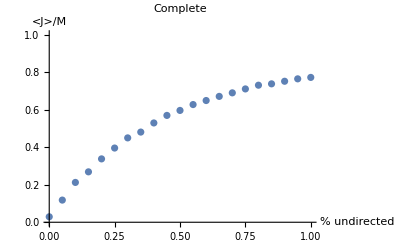

```mathematica
compPlot=ListPlot[toPlot,AxesLabel->{"% undirected","<J>/M"},PlotRange->{All,{0,1}},PlotLabel->"Complete"]
```

### Line

Without restriction (K→ ∞), m=2M

```mathematica
networks=graphToNet[#,fillWith[2M]]&/@line;
```

```mathematica
marbles=Table[netEvolveJ[#,ω,ϕ,i T]&/@networks,{i,5}];
```

```mathematica
toPlot=Table[{(i-1)/20,1/M MeanAround[Rest[marbles[[j]][[i]][[All,2]]]]},{j,5},{i,Length[marbles[[1]]]}];
```

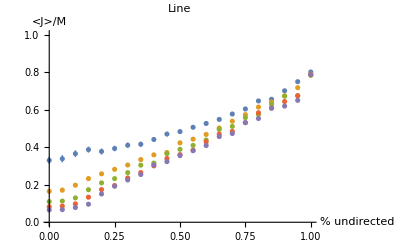

```mathematica
linePlot=ListPlot[toPlot,AxesLabel->{"% undirected","<J>/M"},PlotRange->{All,{0,1}},PlotLabel->"Line"]
```

### Grid

Without restriction (K→ ∞), m=2M

```mathematica
networks=graphToNet[#,fillWith[2M]]&/@grid;
```

```mathematica
marbles=Table[netEvolveJ[#,ω,ϕ,i T]&/@networks,{i,5}];
```

```mathematica
toPlot=Table[{(i-1)/20,1/M MeanAround[Rest[marbles[[j]][[i]][[All,2]]]]},{j,5},{i,Length[marbles[[1]]]}];
```

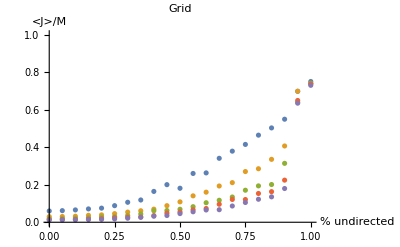

```mathematica
gridPlot=ListPlot[toPlot,AxesLabel->{"% undirected","<J>/M"},PlotRange->{All,{0,1}},PlotLabel->"Grid"]
```

### Scale Free

Without restriction (K→ ∞), m=2M

```mathematica
networks=graphToNet[#,fillWith[2M]]&/@scaleFree;
```

```mathematica
marbles=Table[netEvolveJ[#,ω,ϕ,i T]&/@networks,{i,5}];
```

```mathematica
toPlot=Table[{(i-1)/20,1/M MeanAround[Rest[marbles[[j]][[i]][[All,2]]]]},{j,5},{i,Length[marbles[[1]]]}];
```

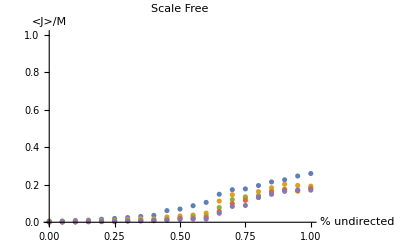

```mathematica
scalePlot=ListPlot[toPlot,AxesLabel->{"% undirected","<J>/M"},PlotRange->{All,{0,1}},PlotLabel->"Scale Free"]
```

### All together

Without restriction (K→ ∞), m=2M

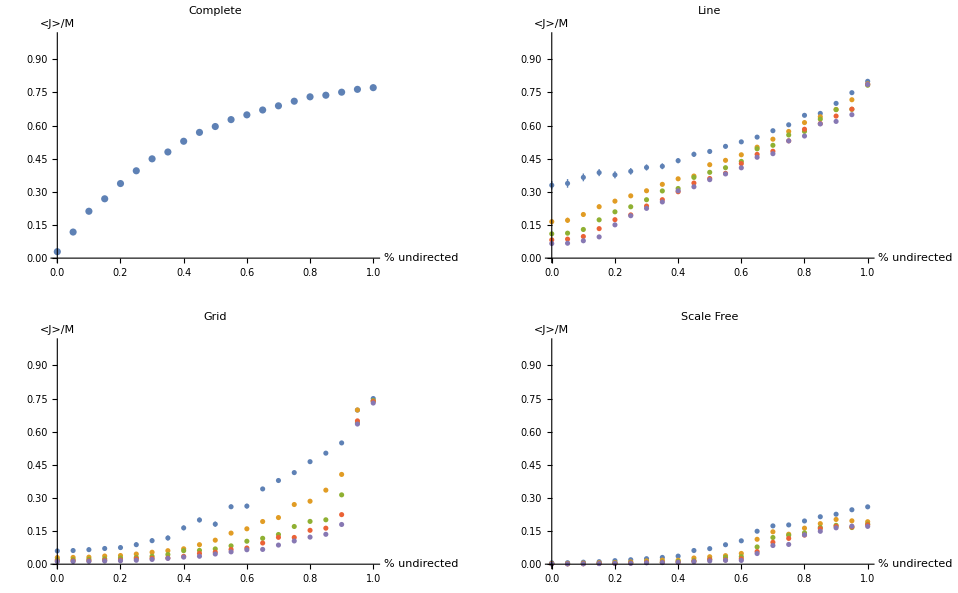

```mathematica
GraphicsGrid[{{compPlot,linePlot},{gridPlot,scalePlot}}]
```

## Variance and distribution of packages

For the different networks calculate the distribution of the number of packages and its variace for the node with the smallest degree (d_min), the average degree (d_avg) and the maximum degree (d_max).

### Complete

```mathematica
degIn=DegreeCentrality[#,"In"]&/@complete;
degOut=DegreeCentrality[#,"Out"]&/@complete;
```

```mathematica
posIn=Table[Flatten[First/@(Position[degIn[[i]],#]&/@({Min[#],Round[Mean[#]],Max[#]}&[degIn[[i]]]))],{i,Length[complete]}];
posOut=Table[Flatten[First/@(Position[degOut[[i]],#]&/@({Min[#],Round[Mean[#]],Max[#]}&[degOut[[i]]]))],{i,Length[complete]}];
```

```mathematica
networks=graphToNet[#,fillWith[2M]]&/@complete;
```

```mathematica
marbles=netEvolve[#,ω,ϕ,T]&/@networks;
```

```mathematica
pIN=Transpose[Table[MeanAround/@(marbles[[i,All,#]]&/@posIn[[i]]),{i,Length[marbles]}]];
pOUT=Transpose[Table[MeanAround/@(marbles[[i,All,#]]&/@posOut[[i]]),{i,Length[marbles]}]];
```

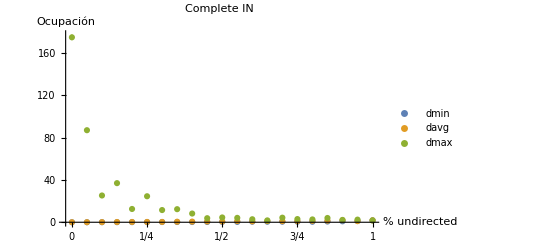
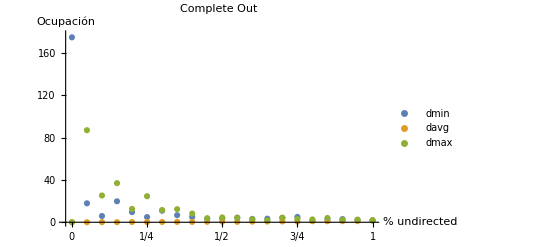
-Graphics- | -Graphics-

```mathematica
Grid[{{ListPlot[pIN,PlotLegends->{"dmin","davg","dmax"},PlotRange->All,Ticks->{Table[{i+1,(i)/20},{i,0,Length[marbles]-1,5}],Automatic},AxesLabel->{"% undirected","Ocupación"},PlotLabel->"Complete\n  IN"],ListPlot[pOUT,PlotLegends->{"dmin","davg","dmax"},PlotRange->All,Ticks->{Table[{i+1,(i)/20},{i,0,Length[marbles]-1,5}],Automatic},AxesLabel->{"% undirected","Ocupación"},PlotLabel->"Complete\n Out"]}}]
```

### Line

```mathematica
degIn=DegreeCentrality[#,"In"]&/@line;
degOut=DegreeCentrality[#,"Out"]&/@line;
```

```mathematica
posIn=Table[Flatten[First/@(Position[degIn[[i]],#]&/@({Min[#],Round[Mean[#]],Max[#]}&[degIn[[i]]]))],{i,Length[line]}];
posOut=Table[Flatten[First/@(Position[degOut[[i]],#]&/@({Min[#],Round[Mean[#]],Max[#]}&[degOut[[i]]]))],{i,Length[line]}];
```

```mathematica
networks=graphToNet[#,fillWith[2M]]&/@line;
```

```mathematica
marbles=netEvolve[#,ω,ϕ,5T]&/@networks;
```

```mathematica
pIN=Transpose[Table[MeanAround/@(marbles[[i,All,#]]&/@posIn[[i]]),{i,Length[marbles]}]];
pOUT=Transpose[Table[MeanAround/@(marbles[[i,All,#]]&/@posOut[[i]]),{i,Length[marbles]}]];
```

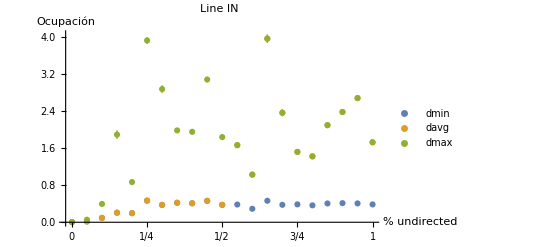
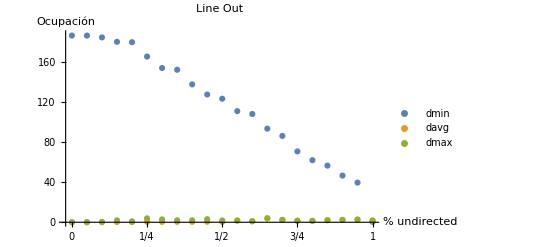
-Graphics- | -Graphics-

```mathematica
Grid[{{ListPlot[pIN,PlotLegends->{"dmin","davg","dmax"},PlotRange->All,Ticks->{Table[{i+1,(i)/20},{i,0,Length[marbles]-1,5}],Automatic},AxesLabel->{"% undirected","Ocupación"},PlotLabel->"Line\n  IN"],ListPlot[pOUT,PlotLegends->{"dmin","davg","dmax"},PlotRange->All,Ticks->{Table[{i+1,(i)/20},{i,0,Length[marbles]-1,5}],Automatic},AxesLabel->{"% undirected","Ocupación"},PlotLabel->"Line\n Out"]}}]
```

### Grid

```mathematica
degIn=DegreeCentrality[#,"In"]&/@grid;
degOut=DegreeCentrality[#,"Out"]&/@grid;
```

```mathematica
posIn=Table[Flatten[First/@(Position[degIn[[i]],#]&/@({Min[#],Round[Mean[#]],Max[#]}&[degIn[[i]]]))],{i,Length[grid]}];
posOut=Table[Flatten[First/@(Position[degOut[[i]],#]&/@({Min[#],Round[Mean[#]],Max[#]}&[degOut[[i]]]))],{i,Length[grid]}];
```

```mathematica
networks=graphToNet[#,fillWith[2M]]&/@grid;
```

```mathematica
marbles=netEvolve[#,ω,ϕ,5T]&/@networks;
```

```mathematica
pIN=Transpose[Table[MeanAround/@(marbles[[i,All,#]]&/@posIn[[i]]),{i,Length[marbles]}]];
pOUT=Transpose[Table[MeanAround/@(marbles[[i,All,#]]&/@posOut[[i]]),{i,Length[marbles]}]];
```

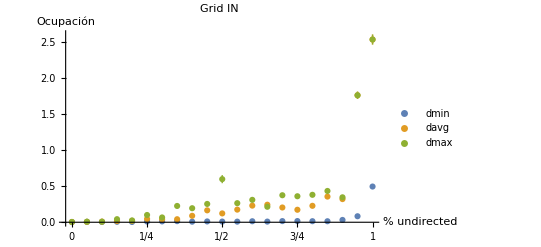
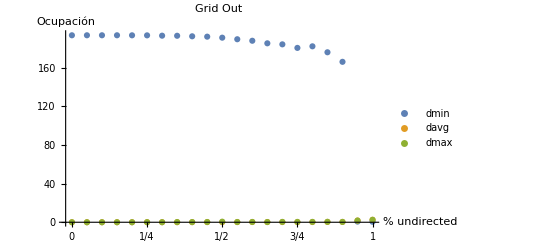
-Graphics- | -Graphics-

```mathematica
Grid[{{ListPlot[pIN,PlotLegends->{"dmin","davg","dmax"},PlotRange->All,Ticks->{Table[{i+1,(i)/20},{i,0,Length[marbles]-1,5}],Automatic},AxesLabel->{"% undirected","Ocupación"},PlotLabel->"Grid\n  IN"],ListPlot[pOUT,PlotLegends->{"dmin","davg","dmax"},PlotRange->All,Ticks->{Table[{i+1,(i)/20},{i,0,Length[marbles]-1,5}],Automatic},AxesLabel->{"% undirected","Ocupación"},PlotLabel->"Grid\n Out"]}}]
```

### Scale Free

```mathematica
degIn=DegreeCentrality[#,"In"]&/@scaleFree;
degOut=DegreeCentrality[#,"Out"]&/@scaleFree;
```

```mathematica
posIn=Table[Flatten[First/@(Position[degIn[[i]],#]&/@({Min[#],Round[Mean[#]],Max[#]}&[degIn[[i]]]))],{i,Length[scaleFree]}];
posOut=Table[Flatten[First/@(Position[degOut[[i]],#]&/@({Min[#],Round[Mean[#]],Max[#]}&[degOut[[i]]]))],{i,Length[scaleFree]}];
posIn[[7]]={6,3,1};
posIn[[8]]={7,3,1};
posIn[[9]]={7,3,1};
posIn[[10]]={7,3,1};
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

```mathematica
networks=graphToNet[#,fillWith[2M]]&/@grid;
```

```mathematica
marbles=netEvolve[#,ω,ϕ,5T]&/@networks;
```

```mathematica
pIN=Transpose[Table[MeanAround/@(marbles[[i,All,#]]&/@posIn[[i]]),{i,Length[marbles]}]];
pOUT=Transpose[Table[MeanAround/@(marbles[[i,All,#]]&/@posOut[[i]]),{i,Length[marbles]}]];
```

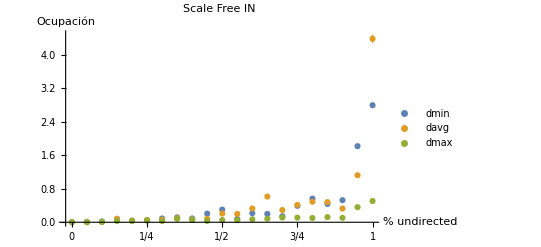
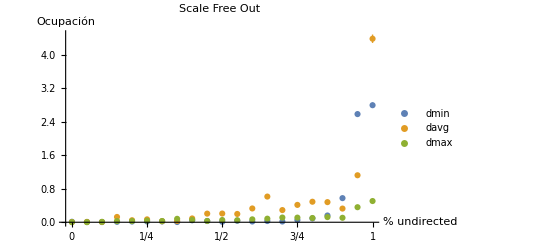
-Graphics- | -Graphics-

```mathematica
Grid[{{ListPlot[pIN,PlotLegends->{"dmin","davg","dmax"},PlotRange->All,Ticks->{Table[{i+1,(i)/20},{i,0,Length[marbles]-1,5}],Automatic},AxesLabel->{"% undirected","Ocupación"},PlotLabel->"Scale Free\n  IN"],ListPlot[pOUT,PlotLegends->{"dmin","davg","dmax"},PlotRange->All,Ticks->{Table[{i+1,(i)/20},{i,0,Length[marbles]-1,5}],Automatic},AxesLabel->{"% undirected","Ocupación"},PlotLabel->"Scale Free\n Out"]}}]
```